Logistic Growth Function and Exponential Growth Function

Introduction to the Logistic Population Model 
(Our focus is actually on the logistic growth function, we just added exponential growth function to compare)
In an ideal world,any species could multiply indefinitely,leading to explosive population growth. Consider a single pair of mice, if they were to reproduce at their maximum biological rate without any constraints, their numbers could reach millions within just a few years. Even more extreme, a single bacterium, such as Staphylococcus aureus, under optimal conditions, could divide every 20 minutes. In just 48 hours, its descendants would weigh more than the entire human population!

However, in reality, we do not see cities overrun by mice or the planet covered in bacterial colonies. This is because population growth is not limitless. Organisms require resources such as food, space, and favorable environmental conditions to survive and reproduce. As populations increase, competition for these limited resources intensifies, leading to slower growth and, eventually, a stabilization in numbers. Ecologists and mathematicians use different models to study population dynamics—how species populations change over time. Some models, such as exponential growth, assume populations grow without limits. Others, like the logistic growth model, account for environmental constraints by introducing a carrying capacity, the maximum number of individuals an environment can sustain. These models are essential for predicting population trends, managing ecosystems, and understanding how species interact with their environments.

Now, we define the Logistic Growth function by first defining their mathematical model. From the exponential growth, we have dN/dt = rN and this produces a J-shaped curve. And from this exponential growth definition, we update it by writing: dN/dt = rN(K - N)/K, that is, dN/dt = rN(1-N/K) where N is the population size, r is the growth rate and K is the carrying capacity

Our interest is in the solved ordinary differential equation, so we define the logistic growth function in Mathematica as follows

This code demonstrates the comparison between two common population growth models:
	-Exponential Growth Model: Assumes unlimited growth without constraints.
	-Logistic Growth Model: Accounts for limited resources and carrying capacity.
We define both models as functions, compute their values for a given time range, and then plot them in three separate figures for comparison. The code includes:
	-The definition of the Logistic Growth function and Exponential Growth function.
	-The computation of population values over time for both models.
	-Generation of three plots:
			1. Logistic Growth function plot 
			2. Exponential Growth function plot 
			3. Comparison of both models in a single plot

Step 1: Define the Logistic Growth Function
The Logistic Growth model accounts for limited resources, where the growth rate slows as the population approaches a carrying capacity (K). The model is given by: dN/dt=rN(1-N/K), with solution: N(t)=K/(1+((K-x0)/x0) Exp[-r t]) where: r=growth rate, K=carrying capacity, x0=initial population size, t=time.

```mathematica
LogisticGrowth[r_, K_, x0_, t_] := K/(1 + ((K - x0)/x0) Exp[-r t]);
```

Step 2: Define the Exponential Growth Function
The Exponential Growth model assumes that the population grows without any constraints,following: dN/dt=rN,with solution:N(t)=N0 Exp[r t] 
where: N0=initial population size,r=growth rate,t=time.

```mathematica
ExponentialGrowth[r_, N0_, t_] := N0 Exp[r t];
```

Step 3:Define Parameters for Both Models
Parameters for growth models:r=growth rate (same for both models for comparison),K=carrying capacity (used in the logistic model),x0=initial population size (used in the logistic model),N0=initial population size (used in the exponential model)

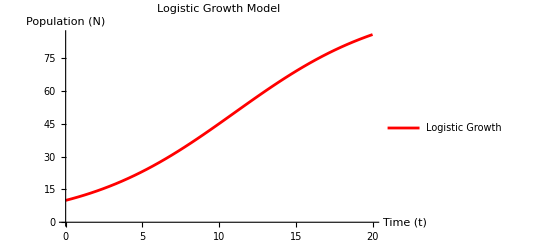
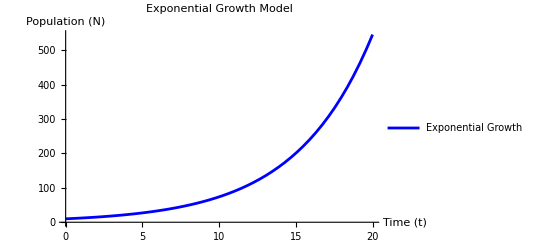
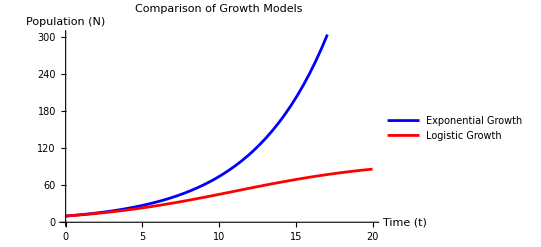

```mathematica
r = 0.2; (*Growth rate*)
K = 100; (*Carrying capacity for Logistic Growth*)
x0 = 10; (*Initial population size for Logistic Growth*)
N0 = 10; (*Initial population size for Exponential Growth*)

(*Step 4:Compute Values for Logistic Growth over time (t=0 to 20)*)
(*Using the Logistic Growth function,we generate a list of population values for each time point.We use a Table to compute these values from t=0 to t=20.*)

logisticValues = Table[{t, LogisticGrowth[r, K, x0, t]}, {t, 0, 20}];

(*Step 5:Compute Values for Exponential Growth over time (t=0 to 20)*)
(*Similarly,we generate the values for the Exponential Growth model using the given growth rate and initial population.This is also computed for t=0 to t=20.*)

exponentialValues = Table[{t, ExponentialGrowth[r, N0, t]}, {t, 0, 20}];

(*Step 6:Plotting the Logistic Growth Function*)
(*The first plot displays the Logistic Growth model over the time range[0,20].*)

plotLogistic = Plot[LogisticGrowth[r, K, x0, t], {t, 0, 20}, PlotLegends -> {"Logistic Growth"}, AxesLabel -> {"Time (t)", "Population (N)"}, PlotLabel -> "Logistic Growth Model", PlotStyle -> {Red}];

(*Step 7:Plotting the Exponential Growth Function*)
(*The second plot shows the Exponential Growth model over the same time range.*)

plotExponential = Plot[ExponentialGrowth[r, N0, t], {t, 0, 20}, PlotLegends -> {"Exponential Growth"}, AxesLabel -> {"Time (t)", "Population (N)"}, PlotLabel -> "Exponential Growth Model", PlotStyle -> {Blue}];

(*Step 8:Plotting Both Models for Comparison*)
(*The third plot compares both models by plotting them together on the same figure.*)

plotComparison = Plot[{ExponentialGrowth[r, N0, t], LogisticGrowth[r, K, x0, t]}, {t, 0, 20}, PlotLegends -> {"Exponential Growth", "Logistic Growth"}, AxesLabel -> {"Time (t)", "Population (N)"}, PlotLabel -> "Comparison of Growth Models", PlotStyle -> {Blue, Red}];

(*Step 9:Display All Three Plots*)
{plotLogistic, plotExponential, plotComparison}
```

Now, Can you tell your observations on each curves? 


Discussion
-The Logistic Growth function is significant because it models population growth with limited resources.
-It is widely used in epidemiology to describe how infectious diseases spread under constraints.
-The domain is R+ (time), and the codomain is (0,K],where K is the carrying capacity.
-N(t) is injective since it passes the horizontal line test.
-The function is often composed with other differential equations in population and epidemic models.
-Mathematica has built-in logistic functions, but we implemented our own for clarity.

Quiz
Write and plot any function of your choice, then upload a screenshot. You are expected to do this during this lab.